```mathematica
(*M=10^15 g and a_*=0*)
```

```mathematica
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));

ϕdetmin[mpbh_?NumericQ,astar_?NumericQ,e_?NumericQ]:=1/(2*π)*(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
ϕdetmax[mpbh_?NumericQ,astar_?NumericQ,e_?NumericQ]:=1/(2*π)*(27*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
```

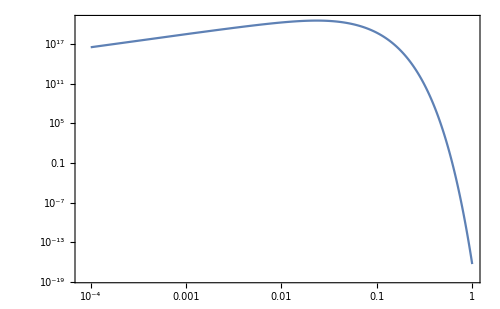

```mathematica
p9999min=ListLogLogPlot[Table[{x,ϕdetmin[10^15,0,x]},{x,10^-4,10^0,0.001}],Joined->True,Frame->True,ImageSize->500]//Quiet
```

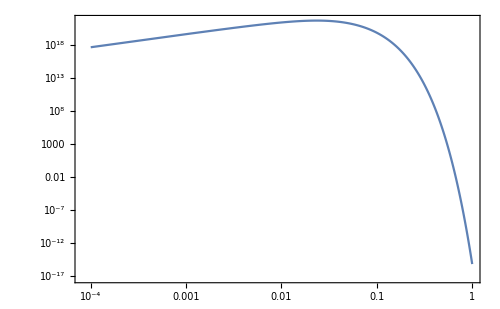

```mathematica
p9999max=ListLogLogPlot[Table[{x,ϕdetmax[10^15,0,x]},{x,10^-4,10^0,0.001}],Joined->True,Frame->True,ImageSize->500]//Quiet
```

```mathematica
data1=Import["instantaneous_primary_spectra_mass1times10power15g_spin0.txt","Table"];
```

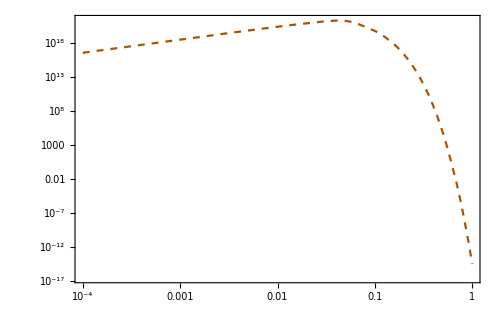

```mathematica
q9999=ListLogLogPlot[Table[{data1[[i,1]],data1[[i,7]]/6},{i,Length[data1]}],PlotRange->{{10^-4,10^0},Automatic},PlotStyle->{Darker[Orange],Dashed},Frame->True,Joined->True,ImageSize->500]
```

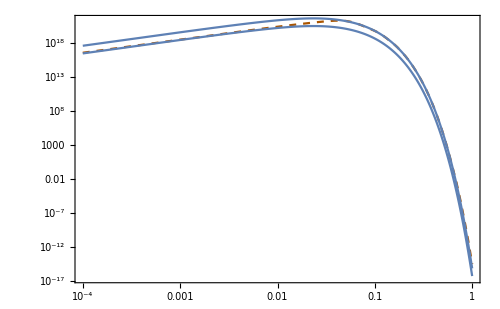

```mathematica
Show[q9999,p9999min,p9999max]
```

```mathematica
(*M=10^15 g and a_*=0.9999*)
```

```mathematica
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));

ϕdetmin[mpbh_?NumericQ,astar_?NumericQ,e_?NumericQ]:=1/(2*π)*(G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-0.5*omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24+1/(2*π)*(G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e+0.5*omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
ϕdetmax[mpbh_?NumericQ,astar_?NumericQ,e_?NumericQ]:=1/(2*π)*(27*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
```

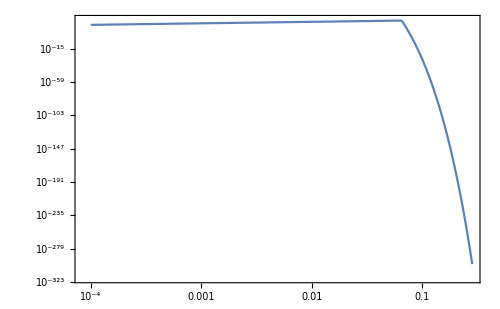

```mathematica
p9999min=ListLogLogPlot[Table[{x,ϕdetmin[10^15,0.9999,x]},{x,10^-4,10^0,0.001}],Joined->True,Frame->True,ImageSize->500]//Quiet
```

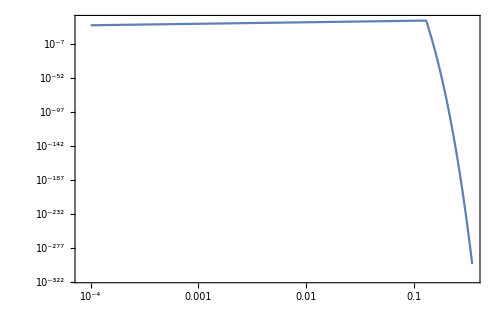

```mathematica
p9999max=ListLogLogPlot[Table[{x,ϕdetmax[10^15,0.9999,x]},{x,10^-4,10^0,0.001}],Joined->True,Frame->True,ImageSize->500]//Quiet
```

```mathematica
data2=Import["instantaneous_primary_spectra_mass1times10power15g_spin0point9999.txt","Table"];
```

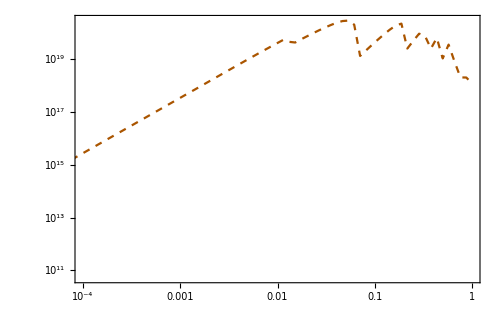

```mathematica
q9999=ListLogLogPlot[Table[{data2[[i,1]],data2[[i,7]]/6},{i,Length[data2]}],PlotRange->{{10^-4,10^0},Automatic},PlotStyle->{Darker[Orange],Dashed},Frame->True,Joined->True,ImageSize->500]
```

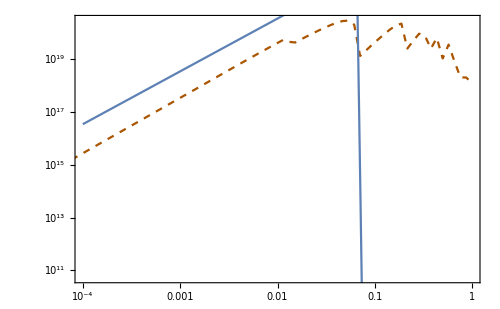

```mathematica
Show[q9999,p9999min]
```

```mathematica
(*M=10^11 g and a_*=0*)
```

```mathematica
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));

ϕdetmin[mpbh_?NumericQ,astar_?NumericQ,e_?NumericQ]:=1/(2*π)*(8*G^2*e^2*mpbh^2*(5.62*10^23)^2*(1+(1-astar^2)^0.5))/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
ϕdetmax[mpbh_?NumericQ,astar_?NumericQ,e_?NumericQ]:=1/(2*π)*(27*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
```

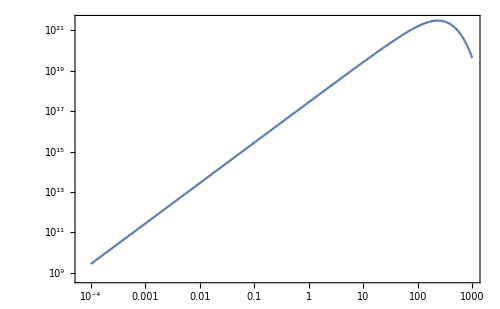

```mathematica
p9999min=ListLogLogPlot[Table[{x,ϕdetmin[10^11,0,x]},{x,10^-4,10^3,0.01}],Joined->True,Frame->True,ImageSize->500]//Quiet
```

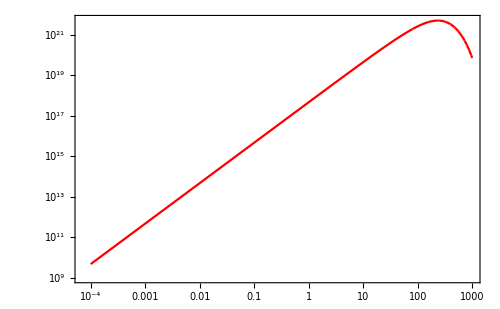

```mathematica
p9999max=ListLogLogPlot[Table[{x,ϕdetmax[10^11,0,x]},{x,10^-4,10^3,0.01}],Joined->True,Frame->True,ImageSize->500,PlotStyle->Red]//Quiet
```

```mathematica
data3=Import["instantaneous_primary_spectra_mass1times10power11g_spin0.txt","Table"];
```

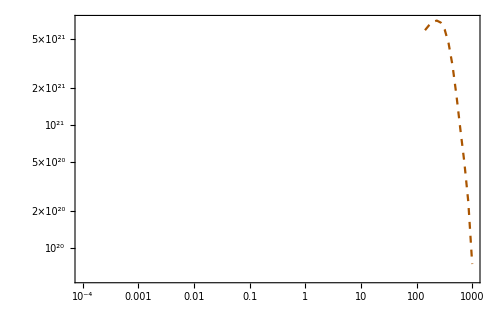

```mathematica
q9999=ListLogLogPlot[Table[{data3[[i,1]],data3[[i,4]]},{i,Length[data3]}],PlotRange->{{10^-4,10^3},Automatic},PlotStyle->{Darker[Orange],Dashed},Frame->True,Joined->True,ImageSize->500]
```

```mathematica
Show[q9999,p9999min,p9999max]
```

-Graphics-

```mathematica
(*M=10^11 g and a_*=0.9999*)
```

```mathematica
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));

ϕdetmin[mpbh_?NumericQ,astar_?NumericQ,e_?NumericQ]:=1/(2*π)*(8*G^2*e^2*mpbh^2*(5.62*10^23)^2*(1+(1-astar^2)^0.5))/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
ϕdetmax[mpbh_?NumericQ,astar_?NumericQ,e_?NumericQ]:=1/(2*π)*(27*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
```

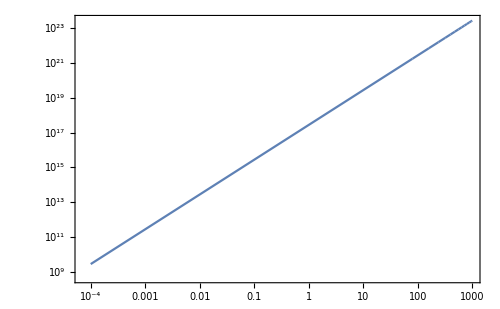

```mathematica
p9999min=ListLogLogPlot[Table[{x,ϕdetmin[10^11,0.9999,x]},{x,10^-4,10^3,0.01}],Joined->True,Frame->True,ImageSize->500]//Quiet
```

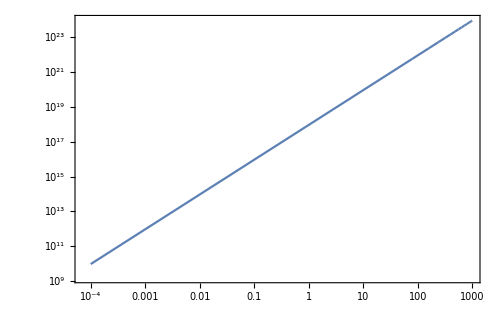

```mathematica
p9999max=ListLogLogPlot[Table[{x,ϕdetmax[10^11,0.9999,x]},{x,10^-4,10^3,0.01}],Joined->True,Frame->True,ImageSize->500]//Quiet
```

```mathematica
data4=Import["instantaneous_primary_spectra_mass1times10power11g_spin0point9999.txt","Table"];
```

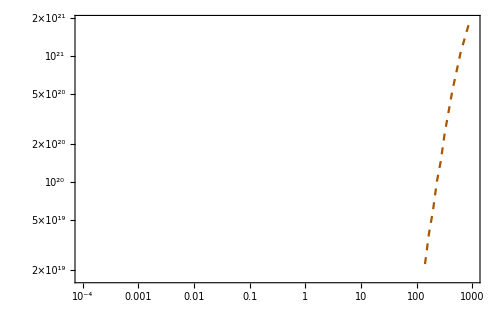

```mathematica
q9999=ListLogLogPlot[Table[{data4[[i,1]],data4[[i,4]]},{i,Length[data4]}],PlotRange->{{10^-4,10^3},Automatic},PlotStyle->{Darker[Orange],Dashed},Frame->True,Joined->True,ImageSize->500]
```

```mathematica
Show[q9999,p9999min,p9999max]
```

-Graphics-